```mathematica
(*ClearAll["Global`*"]*)
```

# Touchstone data importer

## Import and Parsing

```mathematica
filepath="/Users/frankcesco/offline/Radon_Back_End/measurements/taoglas_antenna/tgc200_gnd_ra.s1p";
```

```mathematica
TSFileRaw=Import[filepath,"Table"];
TSFileRawCommentCleaned=Select[TSFileRaw,If[StringQ[#[[1]]],Not[StringStartsQ[#[[1]],"!"]],True]&];
TSFileHeader=TSFileRawCommentCleaned[[1]];
TSData=TSFileRawCommentCleaned[[2;;]];
```

```mathematica
TSFileHeader
```

{#,Hz,S,dB,R,50}

```mathematica
Z0=TSFileHeader[[-1]]
```

50

```mathematica
Y0=1/Z0;
```

```mathematica
FreqMag=Switch[TSFileHeader[[2]]//ToUpperCase,"HZ",0,"KHZ",3,"MHZ",6,"GHZ",9];
TSData[[;;,1]]=TSData[[;;,1]]*10^FreqMag;
```

```mathematica
(*
MA: Magnitude/Degrees Angle
RI: Real/Imaginary
*)
DataType=TSFileHeader[[4]]//ToUpperCase
```

DB

```mathematica
Clear[TSFileRaw,TSFileRawCommentCleaned]; (*clean memory after reading data*)
```

```mathematica
freq=TSData[[;;,1]];
```

## Data Conversion

```mathematica
sReImToComplex[data_]:=Table[#[[2(i-1)+2]]+I#[[2(i-1)+3]],{i,1,(Length[#]-1)/2}]&/@data
sMaDeToComplex[data_]:=Table[#[[2(i-1)+2]]E^(I*2Pi#[[2(i-1)+3]]/360),{i,1,(Length[#]-1)/2}]&/@data
sDBToComplex[data_]:=Table[10^(#[[2(i-1)+2]]/20)E^(I*2Pi#[[2(i-1)+3]]/360),{i,1,(Length[#]-1)/2}]&/@data
sAutoToComplex[data_]:=Switch[DataType,"MA",sMaDeToComplex[data],"RI",sReImToComplex[data],"DB",sDBToComplex[data]]
```

## Transformations

### S to Z Definitions

```mathematica
z11[s11_,s21_,s12_,s22_]:=Z0*((1+s11)(1-s22)+s12 s21)/((1-s11)(1-s22)-s12 s21);
z12[s11_,s21_,s12_,s22_]:=Z0*(2s12)/((1-s11)(1-s22)-s12 s21);
z21[s11_,s21_,s12_,s22_]:=Z0*(2s21)/((1-s11)(1-s22)-s12 s21);
z22[s11_,s21_,s12_,s22_]:=Z0*((1-s11)(1+s22)+s12 s21)/((1-s11)(1-s22)-s12 s21);
```

```mathematica
z11v[sv_]:=z11[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
z12v[sv_]:=z12[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
z21v[sv_]:=z21[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
z22v[sv_]:=z22[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
```

### S to Y Definitions

```mathematica
y11[s11_,s21_,s12_,s22_]:=Y0*((1-s11)(1+s22)+s12 s21)/((1+s11)(1+s22)-s12 s21);
y12[s11_,s21_,s12_,s22_]:=Y0*(-2s12)/((1+s11)(1+s22)-s12 s21);
y21[s11_,s21_,s12_,s22_]:=Y0*(-2s21)/((1+s11)(1+s22)-s12 s21);
y22[s11_,s21_,s12_,s22_]:=Y0*((1+s11)(1-s22)+s12 s21)/((1+s11)(1+s22)-s12 s21);
```

```mathematica
y11v[sv_]:=y11[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
y12v[sv_]:=y12[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
y21v[sv_]:=y21[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
y22v[sv_]:=y22[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
```

### Z to S Definitions

```mathematica
s11[z11_,z21_,z12_,z22_]:=((z11-Z0)(z22+Z0)-z12 z21)/((z11+Z0)(z22+Z0)-z12 z21);
s12[z11_,z21_,z12_,z22_]:=(2Z0 z12)/((z11+Z0)(z22+Z0)-z12 z21);
s21[z11_,z21_,z12_,z22_]:=(2Z0 z21)/((z11+Z0)(z22+Z0)-z12 z21);
s22[z11_,z21_,z12_,z22_]:=((z11+Z0)(z22-Z0)-z12 z21)/((z11+Z0)(z22+Z0)-z12 z21);
```

```mathematica
s11v[sv_]:=s11[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
s12v[sv_]:=s12[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
s21v[sv_]:=s21[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
s22v[sv_]:=s22[sv[[1]],sv[[2]],sv[[3]],sv[[4]]];
```

### Other Network Params

```mathematica
zin[z11_,z21_,z12_,z22_,zl_]:=z11-(z12 z21)/(z22+zl)
```

### Macro Functions

```mathematica
sToZ[data_]:=If[(#//Length)==1,z11v[{#[[1]],0,0,0}],{z11v[#],z12v[#],z21v[#],z22v[#]}]&/@sAutoToComplex[data]
```

```mathematica
sToY[data_]:=If[(#//Length)==1,y11v[{#[[1]],0,0,0}],{y11v[#],y12v[#],y21v[#],y22v[#]}]&/@sAutoToComplex[data]
```

```mathematica
zToS[data_]:=If[(#//Length)==1,s11v[{#[[1]],0,0,0}],{s11v[#],s12v[#],s21v[#],s22v[#]}]&/@data
```

```mathematica
zIn[dataZ_]:=zin[#[[1]],#[[2]],#[[3]],#[[4]],50]&/@sToZ[TSData];
```

## Utilities

```mathematica
conj={Complex[re_,im_]:>Complex[re,-im]};
```

```mathematica
freqAppend[v_]:=Transpose[{freq,v}]
```

## Plots

```mathematica
sToZ[TSData]
```

{4.55781-34.667 ⅈ,4.5858-34.312 ⅈ,10997,15.3417-7.9637 ⅈ,15.3535-7.79517 ⅈ}
 |  |  |  |

```mathematica
myPlotStyle={ImageSize->Large,PlotTheme->"Detailed",PlotRange->All}
```

{ImageSize→Large,PlotTheme→Detailed,PlotRange→All}

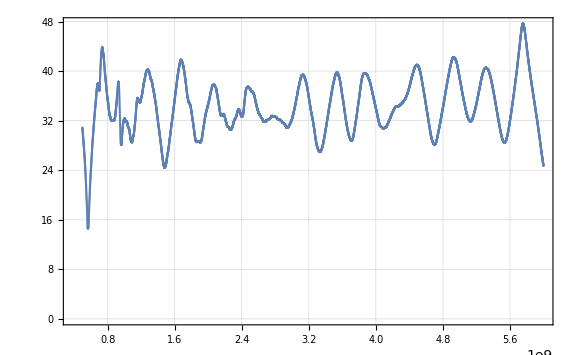

```mathematica
ListPlot[freqAppend[20Log10[sToZ[TSData]//Abs]],myPlotStyle]
```